# Lista V - Física Matemática 1

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.Sousa@usp.br

## 1.a)

Mostrarei que existe uma solução para a equação  i ℏ(∂ψ)/(∂t)= Ĥ ψ , na forma de ψ(t)=e^(-iEt/ℏ)ϕ, para E uma constante indeterminada e ϕ m vetos indeterminado. Onde isso só será verdade se Ĥ  ϕ = E ϕ.
Assim, (∂ψ)/(∂t)=-iE/ℏ e^(-iEt/ℏ)ϕ, substituindo a Eq. na Eq. tenho:
 Ĥ ψ = Ĥ e^(-iEt/ℏ)ϕ= i ℏ(∂ψ)/(∂t)=  E e^(-iEt/ℏ)ϕ ⇔ Ĥ  ϕ = E ϕ

## 1.b)

Para N = 5, ϕ = (ϕ_1, ... , ϕ_N ) , ϕ_(N+1)=ϕ_1 e  ϕ_N=ϕ_0. Mostrarei que a partir da Eq. chagarei na equação de recorrência ϵϕ_n-g ϕ_(n-1)-g ϕ_(n+1)= E ϕ_n. Para Ĥ  = (ϵ | - g | 0 | 0 | - g
- g | ϵ | - g | 0 | 0
0 | - g | ϵ | - g | 0
0 | 0 | - g | ϵ | - g
- g | 0 | 0 | - g | ϵ), assim:
Ĥ  ϕ= (ϵ | - g | 0 | 0 | - g
- g | ϵ | - g | 0 | 0
0 | - g | ϵ | - g | 0
0 | 0 | - g | ϵ | - g
- g | 0 | 0 | - g | ϵ).(ϕ_1 |  
ϕ_2 |  
ϕ_3 |  
ϕ_4 |  
ϕ_5 |  )= (ϵϕ_1 | - gϕ_2 | - g ϕ_5
- g ϕ_1 | + ϵϕ_2 | - g ϕ_3
- g ϕ_2 | + ϵ ϕ_3 | - g ϕ_4
- g ϕ_3 | + ϵ ϕ_4 | - g ϕ_5
- g ϕ_1 | - g ϕ_4 | + ϵ ϕ_5)=(Eϕ_1 |  
Eϕ_2 |  
Eϕ_3 |  
Eϕ_4 |  
Eϕ_5 |  ) . Se você observar com atenção essa matriz, você verá que equação de recorrência já está aparente, por exemplo quando observamos a primeira linha: Eϕ_1 = ϵϕ_1 | - gϕ_2 | - g ϕ_5

## 1.c)

Agora, vou supor que uma solução para  E ϕ_n = ϵϕ_n-g ϕ_(n-1)-g ϕ_(n+1) e da forma ϕ_n= A e^ikn, para k e A constantes indeterminadas. Vou provar a seguir que E = ϵ-2 g cos(k):
E ϕ_n = ϵϕ_n-g ϕ_(n-1)-g ϕ_(n+1) ⇒ E A e^ikn = ϵ A e^ikn-g A e^ikn A e^-ik-g A e^ikn A e^ik ⇒ E = ϵ -g (e^-ik+  e^ik) ⇒ E = ϵ -2g cos(k).

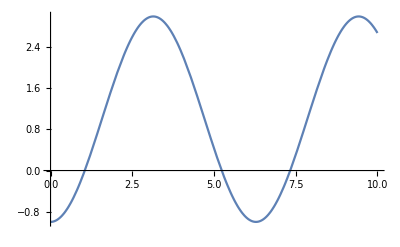

```mathematica
(*Vou supor que ϵ = 1, g = 1 *)
Plot[1 - 2Cos[k],{k,0,10}]
```

```mathematica
(*Dando zoom*)
Plot[1 - 2Cos[k],{k,0,0.5}]
```

```mathematica
λλλλΩΩΩ
```

Para k pequeno, temos que a expansão do cosseno e cos(k)=1 - (k.b2)/2 +..., que expandimos até segunda ordem porque queremos relacioná-la com a relação de dispersão, onde pela equação de borh temos que p = ℏ k e E'=(p.b2)/(2m)=(ℏ.b2k.b2)/(2m). Comparando E e E’, tenho que E = ϵ- 2 g + g k.b2, que desconsiderando a parte constante, temos que:  E'=E =  g k.b2 =(ℏ.b2k.b2)/(2m) ⇔ g =(ℏ.b2)/(2m) ⇔  m =(ℏ.b2)/(2g)

## 1.d)

Aplicando a solução  ϕ_n= A e^ikn na equação ϕ_(N+1)=ϕ_1, temos que:  ϕ_(N+1)=ϕ_1 ⇔ A e^ikN e^ik=A e^ik ⇔  e^ikN=1 ⇔ kN=2π l ⇔ k=(2π l)/N , para l = 0, 1, 2, ..., N-1, se  l fosse até N, teríamos N+1 vetores e o mesmo valor de l para N e 1.
Considerando que  os vetores ϕ_l podem ser normalizados |ϕ_l|.b2=1. Temos então que, para  ϕ_j= A e^ikj :
|ϕ|= ∑_(j=1)^N ϕ_j ϕ_j^*= ∑_(j=1)^N |ϕ_j|.b2= ∑_(j=1)^N |A|.b2=|A|.b2N=1 ⇔ A=1/(√N)

## 3.a)

Usarei o método da serie de potencias, que consiste em uma solução do formato de y(x)=∑_(j=0)^∞ a_j x^j, para encontrar a solução das EDOs a seguir : y''+y=0
→ y'(x)=∑_(j=1)^∞ j a_j x^(j-1) 
→y''(x)=∑_(j=2)^∞ j (j-1)a_j x^(j-2)=∑_(j=0)^∞ (j+2)(j+1)a_(j+2)x^j

y''+y=∑_(j=0)^∞ (j+2)(j+1)a_(j+2)x^j +∑_(j=1)^∞ j a_j x^(j-1)=∑_(j=0)^∞ {(j+2)(j+1)a_(j+2)+ a_j}x^j =0. Isso implica que  (j+2)(j+1)a_(j+2)+ a_j^j deve ser igual a zero. O que nos leva a relação de recorrência: a_(j+2)=-  a_j/((j+2)(j+1)).
Analisando a relação temos que:
→ Para j = 0: 	a_2= - a_0/(2*1) 
→ Para j = 1: 	a_3= - a_1/(3*2) 
→ Para j = 2:	a_4= - a_2/(4*3)=a_0/(4*3*2*1) 
→ Para j = 3:	a_5= - a_3/(5*4)=a_1/(5*4*3*2) 
Portanto, para a_(2j)=((-1)^j a_0)/((2j)!) e a_(2j +1)=((-1)^j a_1)/((2j+1)!) e a nossa será a soma de duas soluções: y(x)=∑_(j=0)^∞ {((-1)^j a_0)/((2j)!)x^(2j)+((-1)^j a_1)/((2j+1)!)x^(2j + 1)}

## 3.b)

Usaremos o mesmo principio para a EDO xy'-y=x.b2
 xy'-y=x.b2⇔  x∑_(j=0)^∞ j a_j x^(j-1)-∑_(j=0)^∞ a_j x^j=x.b2 ⇔   ∑_(j=0)^∞ {j a_j-a_j}x^j=x.b2
 Para j=0: j a_j-a_j=0⇒a_0=0 
 Para j=1: j a_j-a_j=a_1-a_1=0⇒a_j=c_1=constante qualquer 
 Para j=2: j a_j-a_j=2 a_2-a_2=1⇒a_2=1 
 Para j>2: j a_j-a_j=0⇒a_j=0 
 Assim, nossa solução será: y(x)=c_1 x +x.b2

## 4.a)

Usarei a regra de Leibniz,ⅆ^n/(ⅆ x^n)(u.v)=∑_(j=0)^n (n
j)((∂_x)^j u)((∂_x)^(n-j)v) para (n
j)=(n!)/(j!(n-j)!) , para chegar na forma polinomial do polinómio de Laguerre L_n(x)= 1/(n!)e^x ⅆ^n/(ⅆ x^n)(x^n e^-x). Para isso, terei:
→ (∂_x)^j x^n=(n!)/(j!)x^j
→(∂_x)^(n-j)e^-x= (-1)^j e^-x
→ ⅆ^n/(ⅆ x^n)(x^n e^-x) = ∑_(j=0)^n (n
j)(n!)/(j!)x^j (-1)^j e^-x
Assim, tenho que: L_n(x)= ∑_(j=0)^n (n
j)(-x)^j/(j!)

## 4.c)

Vou demonstrar agora uma nova forma de escrever a formula de Rodrigues  L_n(x)= 1/(n!)e^x ⅆ^n/(ⅆ x^n)(x^n e^-x). Para isso, utilizarei o operador D=ⅆ/ⅆx e y=e^-x. Assim:
→ D^n(ye^-x)= D^(n-1)[-ye^-x + e^-x Dy]= D^(n-1)[e^-x (D-1)y]=D^(n-2)[e^-x (D-1).b2y]
Portanto, L_n(x)= 1/(n!)(ⅆ/ⅆx-1)^n x^n

## 4.d)

Agora, vou mostrar que ⅆ/ⅆx L_n(x)=1/(n!)(ⅆ/ⅆx-1)L_(n-1). Para isso usarei que (D(D-1))^n=D(D-1)(D-1)^(n-1) =(D.b2-D)(D-1)^(n-1) . Portanto,
 ⅆ/ⅆx L_n(x)= 1/(n!)(D(D-1))^n x^n = 1/(n!)(D.b2(D-1))^(n-1)x^n -1/(n!)(D(D-1))^(n-1)x^n =  
   1/((n-1)!)(D(D-1))^(n-1)x^(n-1) -1/((n-1)!)(D-1)^(n-1)x^(n-1) = DL_(n-1) - L_(n-1) .
  Assim, ⅆ/ⅆx L_n(x)=1/(n!)(ⅆ/ⅆx-1)L_(n-1)

## 5.a)

Mostrando que ∫_0^∞ e^-x x^m L_n ⅆx = 0, para m<n. Tenho que:
∫_0^∞ e^-x x^m L_n ⅆx = ∫_0^∞ 1/(n!)x^m ⅆ^n/(ⅆ x^n)(x^n e^-x)ⅆx = (-1)^n(m!)/(n!) ∫_0^∞ ⅆ^(n-m)/(ⅆ x^(n-m))(x^m e^-x).
Vou fazer uma integração por partes, onde: ∫uⅆv=uv-∫vⅆu para u = 1, dv=ⅆ^(n-m)/(ⅆ x^(n-m))(x^m e^-x), du = 0, v=ⅆ^(n-m-1)/(ⅆ x^(n-m-1))(x^m e^-x). Assim, usando a regra de Leibniz, tenho:
∫_0^∞ e^-x x^m L_n ⅆx = ⅆ^(n-m-1)/(ⅆ x^(n-m-1))(x^m e^-x)|_0^∞= ∑_(j=0)^n (n
j)((∂_x)^j x^m)((∂_x)^(n-j)e^-x)|_0^∞=
 ∑_(j=0)^n (n
j)(n!)/(j!)(x^(m-j)(-1))^j e^-x|_0^∞=0

## 5.b)

Agora para m = n, faço:
∫_0^∞ e^-x x^n L_n ⅆx =  (-1)^n ∫_0^∞ ⅆ^(n-n)/(ⅆ x^(n-n))(x^n e^-x)=  (-1)^n ∫_0^∞ (x^n e^-x)= (-1)^n n!

## 5.c)

Sabemos que para m<n:  ∫_0^∞ e^-x x^m L_n ⅆx = 0. Para m=n: ∫_0^∞ e^-x x^n L_n ⅆx =  (-1)^n n!.
Analisando a situação onde j<m<n, onde eu chamo L_m=∑_(j=0)^m a_j x^j, tenho que:
∫_0^∞ e^-x L_n L_m ⅆx =∑_(j=0)^m a_j∫_0^∞ e^-x x^j L_n ⅆx = 0
Analisando a situação j≤m=n, tenho que devido ao resultado anterior, só sobrará o enésimo termo na nossa somatória.
∫_0^∞ e^-x L_n L_n ⅆx =∑_(j=0)^n a_j∫_0^∞ e^-x x^j L_n ⅆx =a_n∫_0^∞ e^-x x^n L_n ⅆx
Dá questão 4.a tiramos que L_n(x)= ∑_(j=0)^n (n
j)(-1)^j/(j!)(x)^j → a_j=(n
j)(-1)^j/(j!). Portanto, a_n=(-1)^n/(n!). Assim, usando o resultado do item5.b, temos que:
∫_0^∞ e^-x L_n L_n ⅆx =(-1)^(2n). Ou seja,

∫_0^∞ e^-x L_n L_n ⅆx =δ_nm